```mathematica
ClearAll["Global`*"]
```

```mathematica
training=Transpose[Partition[StringTrim[DeleteStopwords[StringSplit[Import["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\trainingdata.txt"],"\n"]]],2]];
```

```mathematica
c=Classify[Normal[AssociationThread[training[[1]],training[[2]]]],PerformanceGoal->"Quality"]
ClassifierInformation[c]
```

ClassifierFunction[…]

Classifier information
Input type | Text
Classes | ,,essentialextracurricularleisuresportwork
Method | Markov
Accuracy | 69.4 % ± 6.7 %
Loss | 0.794 ± 0.18
Evaluation time | 200. µs/example
Classifier memory | 178. kB
Training examples used | 245 examples
Training time | 2.92 s
 |

```mathematica
api=APIFunction[{"query"->"String"},c[#query]&]
```

APIFunction[{query→String},c[#query]&]

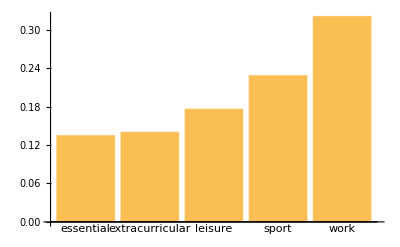

```mathematica
BarChart[c["exercise myself","Probabilities"],ChartLabels->Automatic]
```